```mathematica
μ=0.62;
γ=5/3;
```

```mathematica
years=365.25*86400;
tEnd=10^3 years;
```

```mathematica
rper=0.7Rsun;
θper=45*Pi/180;
kRoss=21.1;
χ=(16*T[Rper,zper]^3*sigmaSB)/(3*kRoss*ρ[Rper,zper]);  (*this is what MB call χ*)
ξradiative =(γ-1)/γ*T[Rper,zper]/P[Rper,zper]*χ     (*this is what MB call ξrad*)

ν=23;   (*from Menou&Balbus2004*)

η=596;     (*from Menou&Balbus2004*)


Timing[Table[θper=θ;
ListofSolutions=Table[

M=Random[Integer,{-12.5,-3.5}];
kRexp=Random[Real,{M-1.5,M+1.5}];
kϕexp=Random[Real,{M-1.5,M+1.5}];
kzexp=Random[Real,{M-1.5,M+1.5}];
kR0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kRexp Rsun);
kϕ0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kϕexp Rsun);
kz0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kzexp Rsun);
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvAexp=Random[Real,{-2,2}];
kdotvA=(-1)^Random[Integer,{0,1}]*10^kdotvAexp*Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vSqmod0=vR0^2+vz0^2;
SolveTheSystem;
vSqmod[t_]=δvRsol[t]^2+δvzsol[t]^2;
MaxVelocitySq=(Max[vSqmod[tEnd/10^6],vSqmod[tEnd/10^5],vSqmod[tEnd/10^4],vSqmod[tEnd/10^3],vSqmod[tEnd/10^2],vSqmod[tEnd/10^1],vSqmod[tEnd]])/vSqmod0;

{kR0,kϕ0,kz0,kdotvA/Ω[Rper,zper],MaxVelocitySq} ,{q,1,100}];

ListofSolutions={θ,Sort[ListofSolutions, #1[[5]] > #2[[5]] &]};
PutAppend[ListofSolutions,"C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\RandomWavevectorTests\\Model B\\Model B - 2 - With Magnetic Field\\Model B with magnetic field - Results.txt"],{θ,5/180 Pi,85/180 Pi,10/180 Pi}]]
```

{109.65625,{Null,Null,Null,Null,Null,Null,Null,Null,Null}}

```mathematica
ListofSolutions
```

{(17 π)/36,{{8.19779×10^-7,9.55649×10^-7,5.38689×10^-8,-0.702997,0.995914},{-9.29761×10^-6,-5.36848×10^-6,5.81079×10^-8,0.0123667,0.970039},{-0.0000566105,4.08359×10^-6,5.7987×10^-7,0.62281,0.969021},{-0.000139183,-0.0000991176,5.2734×10^-6,-0.811394,0.950752},{0.0000520649,0.000197391,3.358×10^-6,0.0484501,0.94166},{-8.09327×10^-7,1.7811×10^-6,-2.61075×10^-7,0.0192193,0.934143},{1.83065×10^-7,-4.66412×10^-6,-3.29445×10^-8,-1.18687,0.920833},{0.000173824,0.0000217157,-0.000284891,-0.503618,0.779299},{0.0000350007,0.000064112,0.0000250814,-0.586635,0.73793},{4.05456×10^-6,-0.0000875902,-0.000112902,0.0259584,0.644942},{8.48231×10^-6,9.57199×10^-6,4.90392×10^-7,-13.1945,0.595656},{0.0000174712,8.682×10^-7,3.07329×10^-6,-27.4871,0.526453},{-0.000042776,-0.000669181,-0.000241433,0.211855,0.471699},{1.25063×10^-6,-5.7636×10^-8,3.25394×10^-7,-1.10886,0.454992},{0.000435666,0.000684142,-0.0000681744,2.50942,0.384662},{5.47449×10^-7,-8.15376×10^-6,1.03795×10^-6,-1.53586,0.280551},{-0.000250139,0.0000584617,0.000936106,2.39506,0.242586},{0.000233814,0.000937444,-0.000245387,7.14338,0.227673},{0.000302267,-0.00101929,0.0000109301,-0.084624,0.190668},{-0.0000229354,0.0000267532,0.00010503,-23.3773,0.138406},{0.0000528203,-0.0000141291,-0.0000265879,11.5924,0.130102},{9.87589×10^-6,-0.0000246333,-7.55652×10^-6,23.743,0.117488},{-0.000103373,-0.0000136623,-0.0000646917,57.8685,0.0870833},{-0.000243089,-5.70493×10^-6,0.000115146,62.5348,0.0857758},{-2.93498×10^-7,6.20726×10^-8,-2.33396×10^-6,19.6146,0.0538037},{6.08813×10^-7,6.62763×10^-6,3.28587×10^-6,0.0243928,0.046135},{0.00125939,0.000792877,-0.000257563,10.5691,0.0367282},{-2.51437×10^-6,-1.80569×10^-7,-1.78199×10^-6,-1.40023,0.017095},{4.91741×10^-6,5.52855×10^-6,-8.77079×10^-6,-57.2534,0.0111529},{1.20012×10^-6,-5.10377×10^-6,7.22215×10^-6,-0.0736277,0.00764799},{-0.0000290854,-0.000135084,-0.00182403,-12.5164,0.00718727},{8.72039×10^-6,-0.00208122,-4.00916×10^-6,2.58805,0.001848},{-0.0000385463,0.0000265758,0.00262457,0.591661,0.0000435721},{0.0000819261,0.000373977,0.00267015,11.2685,0.0000246604},{6.62659×10^-6,-2.5664×10^-7,5.10462×10^-6,0.19173,7.95178×10^-6},{0.0000101289,-4.03543×10^-8,-9.66666×10^-6,-0.178043,1.60164×10^-8},{0.000261516,0.000155214,0.0035094,-0.13036,1.45323×10^-8},{-0.000285456,-0.0000302434,-0.00409206,-0.701826,2.37423×10^-11},{-0.00298615,-0.0043375,-0.00062645,-27.0179,2.75905×10^-17},{-0.0246164,-0.000147002,-0.00390983,9.07422,8.94985×10^-18},{0.0046014,-0.00117881,0.00232184,-0.414535,8.65458×10^-18},{0.0127762,-0.00228907,0.00231386,-0.0949433,2.6631×10^-18},{-0.00665719,-0.000951434,0.000447474,-0.158592,5.04429×10^-19},{-0.00920292,-0.0116443,-0.00614131,-29.4536,2.85585×10^-19},{0.010332,-0.00643521,0.0000906614,96.1748,2.66272×10^-19},{0.0215219,-0.000990485,-0.00110014,0.478904,1.30069×10^-20},{0.0000927202,-0.000110181,0.0061527,-0.0249781,4.70466×10^-21},{-0.0000443076,0.000193093,0.00578413,-6.0643,3.52414×10^-21},{-0.00709424,-0.0289407,-0.111508,-0.167281,1.08335×10^-21},{-0.190183,0.31735,0.333087,3.07842,2.69835×10^-22},{0.0304399,-0.0302944,0.0496819,-1.24972,1.79694×10^-22},{-0.0172067,0.00199702,-0.00547864,-0.175345,1.19175×10^-22},{-0.301304,-0.165898,-0.0150064,-0.0342591,8.80929×10^-23},{-0.00741813,0.000918703,0.018233,-0.0990061,8.76856×10^-23},{-0.00497051,0.00634012,-0.00053053,0.081866,3.79586×10^-23},{-0.0210077,-0.000576771,-0.0000538808,0.265621,1.19964×10^-23},{0.000482664,0.000116839,0.0137275,-0.0457428,6.67828×10^-24},{-0.00024677,-0.000544758,0.0128987,-24.4726,6.44708×10^-24},{0.102931,0.271247,0.0158,-0.11158,3.58712×10^-27},{-0.0141309,-0.00470979,-0.163152,0.0591657,6.39666×10^-28},{0.0723339,-0.0357019,0.138598,-1.29103,1.71914×10^-28},{0.177084,0.366314,0.0363543,0.0418697,1.23712×10^-29},{0.0994719,-2.30871,-0.0437511,-6.2282,4.36532×10^-31},{0.0389778,0.196977,-0.015565,0.183908,1.20646×10^-31},{0.177296,0.525283,-0.0485416,-0.0638831,1.10002×10^-31},{0.0519911,0.0963282,-0.00116416,-0.0221185,3.26281×10^-33},{0.0619035,-0.95085,-0.18596,-6.56063,2.89245×10^-33},{-1.11997,-0.0359787,0.171193,-94.5372,1.49565×10^-39},{0.174695,0.000919744,0.000440517,-0.192912,3.2869×10^-40},{0.199553,-0.00387831,0.400034,-1.93234,5.15847×10^-41},{0.292905,0.401484,-0.829095,-0.0184841,1.06172×10^-41},{-0.82468,0.00906352,-0.276453,-46.6885,3.5739×10^-43},{1.3604,-0.0826577,-0.0405413,25.692,1.17225×10^-43},{0.497362,-0.00809629,0.0485934,-0.0308834,8.69372×10^-45},{2.30326,-0.0981731,-0.0219056,18.2535,4.48156×10^-45},{0.0130338,1.39682,-0.06625,-64.0768,4.46921×10^-45},{-0.010165,-0.00589684,-0.158764,-2.09115,7.45377×10^-46},{2.96688,-2.15416,1.71071,-0.676106,8.30498×10^-48},{-0.0662593,0.271876,0.731682,-13.4561,1.13912×10^-48},{-0.00629921,0.000824901,0.17009,0.03067,4.4291×10^-49},{0.823145,0.24769,-1.26892,-54.1038,6.83306×10^-51},{7.7593,-1.39583,4.00094,-0.0267494,4.05032×10^-52},{-0.0587778,0.000747866,-0.223738,-51.239,1.6555×10^-54},{0.0342105,-0.262289,2.40412,-2.44667,6.44387×10^-55},{-15.5124,14.1313,-0.0379131,-0.0524758,2.92215×10^-55},{19.5117,10.2035,-0.291393,0.0291963,1.88265×10^-56},{-20.4866,-19.197,0.0804625,-0.171088,7.5995×10^-57},{11.3525,4.41362,-0.600236,-0.0138313,3.59141×10^-59},{-29.3843,-6.83407,-0.599808,-8.80744,6.73042×10^-60},{-0.00499511,0.943271,2.81959,-0.0644419,3.58464×10^-71},{14.801,43.3951,-11.4907,0.314936,2.70541×10^-75},{0.0117981,0.00667171,1.97291,-0.241616,8.13089×10^-79},{51.4136,2.25805,-0.5924,56.7568,4.11048×10^-93},{-0.391202,-151.779,2.89207,0.19593,4.49151×10^-101},{-210.124,-10.8861,5.20251,-15.3039,4.29361×10^-101},{365.989,163.571,91.7125,-0.820329,1.47556×10^-106},{3.23341,36.3193,-57.0968,0.309514,6.60569×10^-111},{2154.51,-6.31487,371.284,2.75903,5.70494×10^-167},{32.2294,-108.163,-1902.13,10.5756,1.12729×10^-177},{108.939,-16.5473,-2093.99,0.0481975,1.19819×10^-197}}}

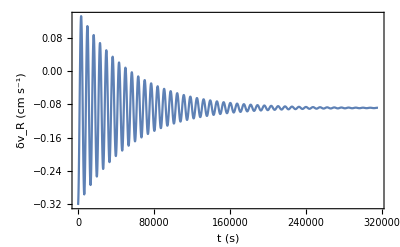

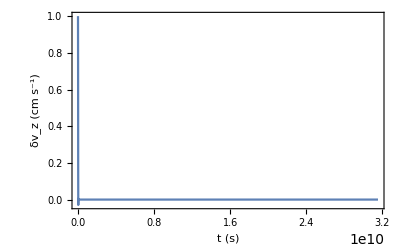

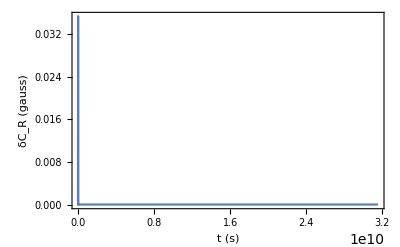

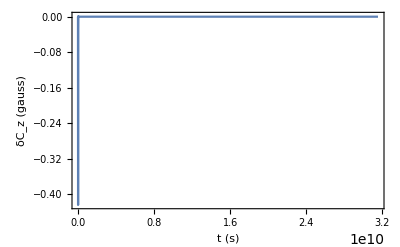

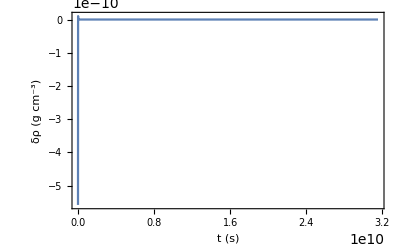

```mathematica
Plot[δvRsol[t],{t,0,tEnd/100000},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_R (cm s^-1)","Test 08 - δv_R(t)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δvzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_z (cm s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCRsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_R (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_z (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δρsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δρ (g cm^-3)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```

```mathematica
kRexp=Random[Real,{M-1.5,M+1.5}];
kϕexp=Random[Real,{M-1.5,M+1.5}];
kzexp=Random[Real,{M-1.5,M+1.5}];
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=100Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

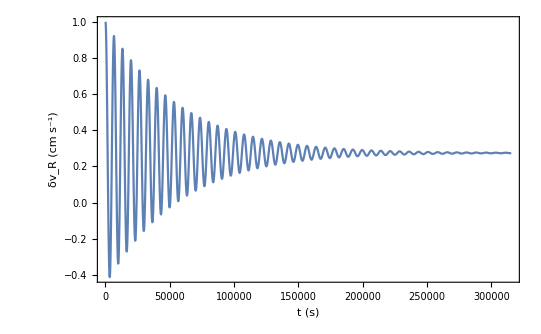

```mathematica
Plot[δvRsol[t]/δvRsol[0],{t,0,tEnd/100000},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_R (cm s^-1)","Test 08 - δv_R(t)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```